```mathematica
c=2.9979*^8;
ℏ=1.05*^-34;
k=1.3806*^-23;
ℏc=ℏ c;

γ[side_]:=Block[{},
Switch[side,
1,4.521*^13,
2,0,
_,0
]
]
ωp[side_]:=Block[{},
Switch[side,
1,1.37*^16,
2,8.85938*^15,
_,0
]
]
ϵinf[side_]:=Block[{},
Switch[side,
1,1,
2,1.035,
_,0
]
]
ϵ0[side_]:=Block[{},
Switch[side,
1,0,
2,11.87,
_,0
]
]

ϵi[ω_, model_, side_]:=Block[{},
Switch[model,
1,1+(ωp[side]/ω)^2,
2,Switch[side,
1,1+ωp[side]^2/(ω(ω+γ[side])), (* Drude Model *)
2,ϵinf[side]+(ϵ0[side]-ϵinf[side])/(1-(ω/ωp[side])^2) (* Dielectric Model *),
_,0
],
_,0
]
]

r[ω_,κ_,pol_,model_,side_]:=Block[{ϵr,l,r},
ϵr=ϵi[ω,model,side];
l=Sqrt[ω^2*(ϵr-1)+c^2κ];
r=Switch[pol,
1,c κ,
2,c κ*ϵr
];
Return[(l-r)/(l+r)]
]
rsquared[ω_,κ_,pol_,model_]:=r[ω,κ,pol,model,1]*r[ω,κ,pol,model,2]

ωIntegral[κ_,model_,L_]:=Block[{},
integ[lim_?NumberQ]:=NIntegrate[(Log[1-rsquared[ω,κ,1,model]*Exp[-2*κ*L]]+Log[1-rsquared[ω,κ,2,model]*Exp[-2*κ*L]]),{ω,0,lim},AccuracyGoal->3];
integ[c*κ]
]

ηE[model_,L_]:=Block[{},
-((180.0*L^3)/(c*Pi^4))NIntegrate[κ*ωIntegral[κ,model,L],{κ,10.^-1,1.6*^7},AccuracyGoal->3]
]
```

```mathematica
(* Plot Conductivity Models *)
ϵs=Flatten[Table[ϵi[ω,i,j],{i,1,2},{j,1,2}]];
```

```mathematica
ηplasma=Table[{10.0^exp,ηE[1,10.0^(exp)]},{exp,-7,-4,0.1}];
```

```mathematica
ηdrude=Table[{10.0^exp,ηE[2,10.0^(exp)]},{exp,-7,-4,0.1}];
```

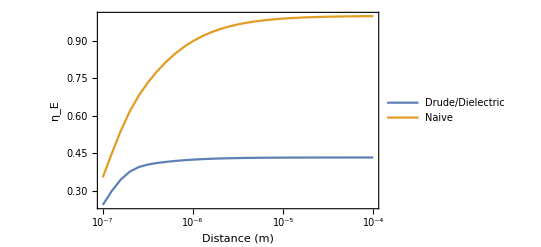

```mathematica
ListLogLinearPlot[{ηdrude,ηplasma},Frame->True,PlotRangePadding->{None,0.1},FrameLabel->{"Distance (m)","η_E"},ImageSize->Scaled[0.8],Joined->True,PlotLegends->{"Drude/Dielectric","Naive"}]
```

```mathematica
Eperfect[L_,R_]:=Block[{},
-(Pi^3ℏ c/720.)(R/(L^2))(1.+0.3333333(L/R))
]

Fperfect[L_,R_]:=Block[{},
(2ℏ c Pi^3/720)*(R/(L^3))*(1+(0.3333333/2.0)*L/R)
]

FPFA[L_,R_]:=Block[{},
(2ℏ c Pi^3/720)*(R/(L^3))
]

ηplasmaInterp=Interpolation[ηplasma];
ηdrudeInterp=Interpolation[ηdrude];
ηInterp[model_,L_]:=Block[{},
Switch[model,
1,ηplasmaInterp[L],
2,ηdrudeInterp[L],
_,0
]
]

ψ[L_,r_,R_]:=R (1-Sqrt[1-r^2/R^2])+L
dψsq[r_,R_]:=1/((R^2/r^2)-1)
Integrand[model_,L_,r_,R_]:=Block[{},
(ηInterp[model,ψ[L,r,R]]/(ψ[L,r,R]^3))(1+(1/3)dψsq[r,R])
]
Integrand0[model_,L_,r_,R_]:=Block[{},
(1/(ψ[L,r,R]^3))(1+(1/3)dψsq[r,R])
]

Ec[model_,L_,R_]:=Block[{},
intval[Lval_?NumericQ]:=NIntegrate[Integrand[model,Lval,r,R],{r,0.0,0.5R},AccuracyGoal->2];
-(2Pi^3 ℏ c/720.)*intval[L]
]

Fc[model_,L_,R_]:=Block[{},
Limit[(Ec[model,L+x,R]-Ec[model,L,R])/x,x->0]
]

fTemp[T_,L_]:=Block[{ξ},
ξ=k*T*L/(ℏ c);
If[ξ≤ 0.5,
(ξ^3/(2Pi))*1.202-(ξ^4Pi^2/45),(ξ/(8Pi))*1.202-(Pi^2/720)
]
]
TempCorrection[T_,L_]:=Block[{},
1.+(720./Pi^2)*fTemp[T,L]
]

FPFAcorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*FPFA[L,R]*TempCorrection[T,L]
]

Fcorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*Fperfect[L,R]*TempCorrection[T,L]
]
Ecorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*Eperfect[L,R]*TempCorrection[T,L]
]

b={-9/16,0,-25/32,-3023/4096,-12551/9600,1282293/163840,-32027856257/722534400,39492614653/412876800}//N;

EEmigFar[L_,R_]:=ℏc/(Pi (L+R))*Sum[b[[i]]*(R/(L+R))^(i+2),{i,1,Length[b]}];

θ1=-1.42;
θ2=2.49;
EEmigNear[L_,R_]:=-(Pi^3/720)ℏc*R/L^2*(1+θ1*L/R+θ2*L^2/R^2)//Expand;

FEmigFar[L_,R_]:=D[EEmigFar[x,R],x]/.x->L;
FEmigNear[L_,R_]:=D[EEmigNear[x,R],x]/.x->L;
```

```mathematica
radius=2.5*^-6;

FEmigFarMicron[l_]:=FEmigFar[l*10^(-6),radius];
FEmigNearMicron[l_]:=FEmigNear[l*10^(-6),radius];

nearLog=Table[{Log[l],Log[FEmigNearMicron[l]*10^18]},{l,0.1,0.5,.1}];
farLog=Table[{Log[l],Log[FEmigFarMicron[l]*10^18]},{l,10,30}];
range=Join[nearLog,farLog];

FInterp=Interpolation[range];
FEmig[L_]:=Exp[FInterp[Log[L]]];

FEmigCorrected[model_,L_,T_]:=ηInterp[model,L*10^(-6)]*FEmig[L]*TempCorrection[T,L*10^(-6)];
```

```mathematica
near=Table[{l,FEmigNearMicron[l]*10^18},{l,0.1,0.5,.05}];
far=Table[{l,FEmigFarMicron[l]*10^18},{l,10,30}];
```

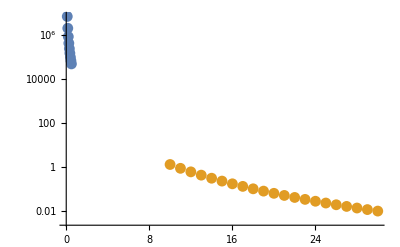

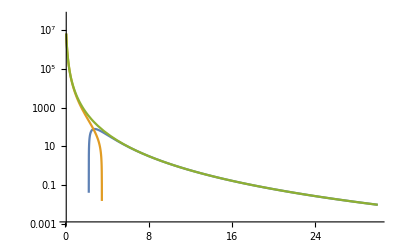

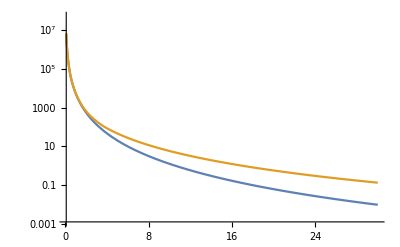

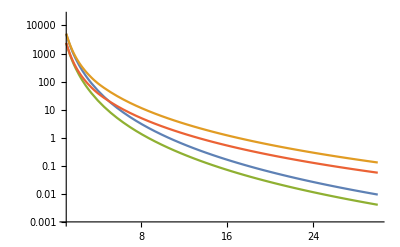

```mathematica
range=Join[nearLog,farLog];
f=Interpolation[range];
ListLogPlot[{near,far}]
LogPlot[{FEmigFarMicron[l]*10^18,FEmigNearMicron[l]*10^18,Exp[f[Log[l]]]},{l,.1,30}]
LogPlot[{FEmig[l],FEmig[l]*TempCorrection[300,l*10^(-6)]},{l,.1,30}]
LogPlot[{FEmigCorrected[1,l,0],FEmigCorrected[1,l,300],FEmigCorrected[2,l,0],FEmigCorrected[2,l,300]},{l,1,30}]
```

```mathematica
data=Table[{l,FEmigCorrected[1,l,0],FEmigCorrected[1,l,300],FEmigCorrected[2,l,0],FEmigCorrected[2,l,300]},{l,.1,30,0.01}]
Export[NotebookDirectory[]<>"calculated_exp_vals.tsv",data];
```

{{0.1,2.32571×10^6,2.32578×10^6,1.5988×10^6,1.59885×10^6},{0.11,1.93868×10^6,1.93876×10^6,1.31549×10^6,1.31554×10^6},2987,{29.99,0.00982476,0.135263,0.00426677,0.058743},{30.,0.00980958,0.135099,0.00426018,0.0586717}}
 |  |  |  |